```mathematica
ParallelEvaluate[Off[General::munfl,FindFit::cvmit]];
Off[General::munfl,General::stop,LinearSolve::luc,FindFit::cvmit]
SetDirectory[NotebookDirectory[]]
```

/home/kirscher/kette_repo/limit_cycles/manuscript/graphs

```mathematica
hbarc=197.327053;
Mm=938.858;
m1=2 Mm;m2=2 Mm;
μ=m1 m2/(m1+m2);
mh2=(2 μ)/(hbarc)^2;
Print["ℏ^2/(2  μ) = ",1/mh2]
cijTh=10^-12;
dbg=False;
```

ℏ^2/(2  μ) = 20.7369

Read LEC list (e.g. fitted to two-body scattering length via <<<Fit_Scattering_length.nb>>>)

```mathematica
activeLEC=Select[Import["/home/kirscher/Documents/vault/Vorlesungen/num_methods/lec_ex0_b2.22.dat","Table"][[2;;]],#[[3]]!=-131.&];
line=Fit[Transpose[{activeLEC[[All,1]],activeLEC[[All,2]]}],{1,x},x]
fittedLECs=Table[{λ,line/.x->λ},{λ,Range[activeLEC[[All,1]][[1]],10 activeLEC[[All,1]][[-1]],90]}];
activeLEC=activeLEC[[;;;;10]]
activeLEC=fittedLECs
```

-104.498-113.163 x

{{8.,-974.194,-1105.1,0.},{18.,-2128.1,-1711.48,4.29},{28.,-3271.38,-1912.15,5.08},{38.,-4409.67,-1973.3,5.62},{48.,-5545.3,-1.,0.},{58.,-6678.68,-1.,0.},{68.,-7810.85,-1.,0.},{78.,-8941.35,-1.,0.},{88.,-10072.4,-1.,0.},{98.,-11203.3,-1.,0.},{108.,-12327.4,-1.,0.},{118.,-13452.5,-1.,0.},{128.,-14584.2,-1.,0.},{138.,-15704.3,-1.,0.}}

{{8.,-1009.8},{98.,-11194.5},{188.,-21379.1},{278.,-31563.8},{368.,-41748.4},{458.,-51933.1},{548.,-62117.8},{638.,-72302.4},{728.,-82487.1},{818.,-92671.7},{908.,-102856.},{998.,-113041.},{1088.,-123226.},{1178.,-133410.},{1268.,-143595.},{1358.,-153780.}}

```mathematica
(*one dimer to rule them all*)
eCore=2.2;
ScaleFac=1.;
dimerCore=Get["UnivDimerWFI"]
(*If[Length[dimerCore]==1,ScaleFac=1./dimerCore[[1]][[1]];]*)
dimerCore=Transpose[{ScaleFac dimerCore[[All,1]],ScaleFac dimerCore[[All,2]]}]
```

{{0.0875605,0.159053},{0.0841116,0.0152572}}

{{0.0875605,0.159053},{0.0841116,0.0152572}}

```mathematica
RiccatiBesselJ=Compile[{z,l},z SphericalBesselJ[l,z]];
RiccatiBesselN=Compile[{z,l},(-1)^l z SphericalBesselY[l,z]];
```

```mathematica
(*Boundery conditions for the wavefunction*)
alpha=Compile[{ra,ka,la,ha},RiccatiBesselN[ka (ra+ha),la]/RiccatiBesselN[ka ra,la]];

beta=Compile[{rb,kb,lb,hb},RiccatiBesselJ[kb (rb+hb),lb]-RiccatiBesselJ[kb rb,lb] (RiccatiBesselN[kb (rb+hb),lb]/RiccatiBesselN[kb rb,lb])];
```

reference: J. Spanier, K.B. Oldham - An Atlas of Functions (1987)

x·j_n(x)=√((π x)/2)J_(n+1/2)(x)=^(x∈C)√((π x)/2)i^(n+1/2) I_(n+1/2)(Re[x])
with
 j_n: spherical Bessel (1st kind)
 J_n: Bessel (1st kind)
 I_n: modified Bessel (1st kind)
 to optimize runtime, we substitute in this implementation -- valid for S-wave scattering, only:
 j_0(i x)=Sinh[x]/x
 and
 j_1(i x)=i x^-1(Cosh[x]-Sinh[x]/x)
 For numerical stability at arguments x>>1, it is curucial to subsitute the following representation:
 e^(-aR^2-bR'^2) Sinh[bRR']=1/2(e^(-aR^2-bR'^2+bRR')-e^(-aR^2-bR'^2-bRR')) and similarly for the hyperbolic cosine;
 Retaining the Sinh built-in function throws, at best, warnings, and yields significantly inaccurate and almost certainly non-sensical results!

```mathematica
VlocTF=Compile[{r,lam,Cc,Dd,Aa,Bb,Gg,Hh},Block[{eta2,eta3,w2,w3},
eta2=Cc (2 (Aa+Bb)(Gg+Hh)/(lam Bb + Aa(lam + 2Gg +2  Bb) + lam Hh +2 Bb Hh+Gg(lam +2Hh)))^(3/2);
w2= 2lam(Aa+Hh)(Gg+Bb)/(lam Bb + Aa(lam+2 Gg+2Bb)+lam Hh +2 Bb Hh+Gg(lam+2Hh));
eta3 =Cc (2 (Aa+Bb)(Gg+Hh)/(lam Bb + Gg(lam + 2Bb)+lam Hh +2Bb Hh + Aa(lam+2Gg+2Hh)))^(3/2);
w3 = 2lam(Aa+Bb)(Gg+Hh)/(lam Bb + Gg(lam+2Bb)+lam Hh +2Bb Hh+Aa(lam+2Gg+2Hh));
eta2 Exp[-w2 r^2]+eta3 Exp[-w3 r^2]
]];

WnolocTF3=Compile[{r,rp,Ee,lam,Cc,Dd,Aa,Bb,Gg,Hh,Ll,TwoMyOverHBsq},Block[{zeta1,zeta2,zeta3,a1,b1,c1,a2,b2,c2,a3,b3,c3,Sinh1,Sinh2,Sinh3,CoshA},
zeta1=-8 ((Aa+Bb)(Gg+Hh)/(Aa+Bb+Gg+ Hh))^(3/2) (1/TwoMyOverHBsq);
a1=(4Bb Hh + Gg Bb+Gg Hh+Aa Bb +Aa Hh)/(2Aa+2Bb+2Gg+2Hh);
b1=(2Gg Bb -2Gg Hh -2 Aa Bb +2 Aa Hh)/(2Aa+2Bb+2Gg+2Hh);
c1=(Gg Bb +Hh Gg+4Aa Gg +Aa Bb +Aa Hh)/(2Aa+2Bb+2Gg+2Hh);

zeta2=-32 Cc((Aa+Bb)(Gg+Hh)/(2lam+Aa +Bb+ Gg+Hh))^(3/2);
zeta3=-32 Cc((Aa+Bb)(Gg+Hh)/(2lam+Aa +Bb+ Gg+Hh))^(3/2);

a2=(4Hh(2lam+Bb)+Gg(2lam +Bb+Hh)+Aa(2lam+Bb+Hh))/(2(2 lam+Aa+Bb+Gg+Hh));
b2=(Gg(4 lam+2 Bb-2 Hh)+Aa (-4 lam-2 Bb+2 Hh))/(2 (2 lam+Aa+Bb+Gg+Hh));
c2=( Gg(2lam+Bb+Hh)+Aa(2lam+4Gg+Bb+Hh))/(2(2 lam+Aa+Bb+Gg+Hh));

a3= (4Bb(2lam+Hh)+Gg(Bb+2lam+Hh)+Aa(2lam+Bb+Hh))/(2(2 lam+Aa+Bb+Gg+Hh));
b3=(Gg(2Bb-4lam-2Hh)+Aa(4lam+2Hh-2Bb))/(2(2 lam+Aa+Bb+Gg+Hh));
c3=(Gg(Bb+2lam+Hh)+Aa(4Gg+2lam+Bb+Hh))/(2(2 lam+Aa+Bb+Gg+Hh));

(-4 Pi r rp) (zeta1 Exp[-a1 r^2-c1 rp^2] (-(4 a1^2 r^2-2 a1)- TwoMyOverHBsq Ee)+zeta2 Exp[-a2 r^2-c2 rp^2]+zeta3 Exp[-a3 r^2-c3 rp^2])
]];
```

```mathematica
SphericalBesselJ[0,0]
```

1

```mathematica
SolveSecularP3[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ,Lin_?NumberQ,lam_?NumberQ,c0_?NumberQ,d0_?NumberQ,a00_?ArrayQ,TwoMyOverHBsq_?NumberQ]:=Block[{hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,wf,tanDelta,usol,energyMeV,nff,cij},
t1=AbsoluteTime[];
hDif=Rdis/Npoints;
energyMeV=(momentum^2)/TwoMyOverHBsq;
Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{Npoints,Npoints}];

Wmats={};
SetSharedVariable[Wmats];

ParallelDo[

cij=a00[[ii]][[1]] a00[[jj]][[1]] a00[[kk]][[1]] a00[[ll]][[1]];
(*cij=0.0;*)

amat=DiagonalMatrix[Table[-hDif^2 TwoMyOverHBsq VlocTF[i hDif,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]],a00[[kk]][[2]],a00[[ll]][[2]]],{i,1,Npoints}]];

wmat=Table[-hDif^3 TwoMyOverHBsq WnolocTF3[i hDif,j hDif,energyMeV,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]],a00[[kk]][[2]],a00[[ll]][[2]],Lin,TwoMyOverHBsq],{i,1,Npoints},{j,1,Npoints}(*,ProgressReporting->False*)]; 

AppendTo[Wmats,cij (amat+wmat)];
(*AppendTo[Wmats,cij amat];*)

,{ii,1,Length[a00]},{jj,1,Length[a00]},{kk,1,Length[a00]},{ll,1,Length[a00]}];

Wmat=Total[Wmats];
Dmat=DiagonalMatrix[Table[hDif^2 (momentum^2),{i,1,Npoints}]];

Amat=Kmat+Dmat+Wmat;

bcol=ConstantArray[0,Npoints];
ucol=Array[Subscript["u", ##]&,{Npoints}];

bcol⟦-1⟧=- beta[Rdis,momentum,Lin,hDif];
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+alpha[Rdis,momentum,Lin,hDif];

usol=LinearSolve[Amat,bcol];
relerr=Norm[Amat.usol-bcol]/Norm[usol];
(*Print["relative error in wave-function solution = ",relerr];*)

(*tanDelta= (RiccatiBesselJ[momentum Rdis,Lin]/RiccatiBesselN[momentum Rdis,Lin])-(usol⟦-1⟧/RiccatiBesselN[momentum Rdis,Lin]);*)
sol=NSolve[usol⟦-1⟧==RiccatiBesselJ[momentum Rdis,Lin]-RiccatiBesselN[momentum Rdis,Lin] xx,xx,Reals];
tanDelta=xx/.sol[[-1]];
t2=AbsoluteTime[];
(*Print["finite-difference runtime Δt = ",(t2-t1)/60.," mins     p_match·r_max = ",momentum Rdis];*)
{tanDelta,usol}
];
```

```mathematica
GetEREP3[l_,rMax_,nPoints_,core_,LECc_,energ_:0.01]:=Module[{locall=l},
LECd=0.0;
momFM=Sqrt[mh2 energ];
{TanDelSwave,wfkt}=SolveSecularP3[rMax,nPoints,momFM,0,locall,LECc,LECd,core,mh2];
{-TanDelSwave/Sqrt[mh2 energ ],wfkt}
]
```

alternative to the stochastic and inefficient search for an appropriate basis, one can invoke a genetic optimization (external Python/Fortran program, look for <bridgeA2_tmp.py> and calls therein)
and feed the results to the function <CalcDimerE[]> (see above

Using λ=8.fm^-2     C=-1009.8MeV  which is renormalized to B(dimer)=2.2MeV

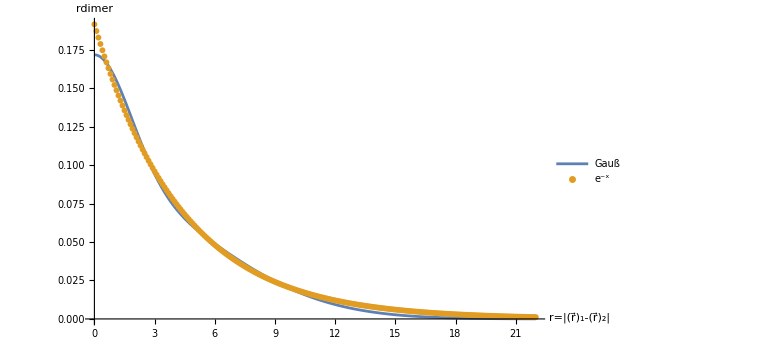

```mathematica
lambdas=activeLEC[[All,1]];
lambdaTest=lambdas[[1]];
LECc=Flatten[Select[activeLEC,#[[1]]==lambdaTest&]][[2]];
Print["Using λ=",Style[lambdaTest,Red],"fm^-2     C=",Style[LECc,Red],"MeV  which is renormalized to B(dimer)=",Style[eCore,Red],"MeV"];

JacobiTrailWavefunctionU=Total[#[[1]] Exp[-#[[2]] r1^2]&/@dimerCore];rR=Range[0,22,0.100];
JacobiTrailWavefunctionDataU=Table[JacobiTrailWavefunctionU/.{r1->R1},{R1,rR}];

plotData=Transpose[{rR,JacobiTrailWavefunctionDataU}];
plotDataExp=Table[{rr,√((√(Mm eCore))/(2 π hbarc))Exp[-(√(Mm eCore))/hbarc rr]},{rr,rR}];
lgd={"Gauß","e^-x"};

ListPlot[{Transpose[{rR,plotData[[All,2]]}],Transpose[{rR,plotDataExp[[All,2]]}]},AxesLabel->{"r=|(r⃗)_1-(r⃗)_2|","TemplateBox[{\"r\", \"dimer\"},\"BraKet\"]"},PlotLegends->lgd,ImageSize->Large,PlotLabels->Automatic,Joined->{True,False}]
```

```mathematica
(* energy at which the scattering length is obtained from the amplitude *)
energ=0.1;
(* Integration grid *)
rMa=14;
grdPerFermi=13;
nGrd=IntegerPart[rMa grdPerFermi];
results={};

Do[
LECc=Flatten[Select[activeLEC,#[[1]]==lam&]][[2]];
tmp=GetEREP3[lam,rMa,nGrd,dimerCore,LECc,energ][[1]];
AppendTo[results,{lam,LECc,rMa,nGrd,eCore,tmp,tmp/(hbarc/√(Mm Abs[eCore]))}];
Print["λ=",lam," B(2)=",eCore,"  C_0(λ)=",LECc,")  ; R_max=",rMa," ; #=",nGrd," ; E_match=",energ," ; a_dd=",tmp," ; a_dd/a_aa=",tmp/(hbarc/√(Mm Abs[eCore]))];
,{lam,lambdas}];
```

λ=8. B(2)=2.2  C_0(λ)=-1009.8)  ; R_max=14 ; #=182 ; E_match=0.1 ; a_dd=-0.795369 ; a_dd/a_aa=-0.183186

λ=98. B(2)=2.2  C_0(λ)=-11194.5)  ; R_max=14 ; #=182 ; E_match=0.1 ; a_dd=-0.515416 ; a_dd/a_aa=-0.118709

λ=188. B(2)=2.2  C_0(λ)=-21379.1)  ; R_max=14 ; #=182 ; E_match=0.1 ; a_dd=-0.488908 ; a_dd/a_aa=-0.112603

λ=278. B(2)=2.2  C_0(λ)=-31563.8)  ; R_max=14 ; #=182 ; E_match=0.1 ; a_dd=-0.476849 ; a_dd/a_aa=-0.109826

λ=368. B(2)=2.2  C_0(λ)=-41748.4)  ; R_max=14 ; #=182 ; E_match=0.1 ; a_dd=-0.469591 ; a_dd/a_aa=-0.108154

λ=458. B(2)=2.2  C_0(λ)=-51933.1)  ; R_max=14 ; #=182 ; E_match=0.1 ; a_dd=-0.464613 ; a_dd/a_aa=-0.107008

λ=548. B(2)=2.2  C_0(λ)=-62117.8)  ; R_max=14 ; #=182 ; E_match=0.1 ; a_dd=-0.460928 ; a_dd/a_aa=-0.106159

λ=638. B(2)=2.2  C_0(λ)=-72302.4)  ; R_max=14 ; #=182 ; E_match=0.1 ; a_dd=-0.458059 ; a_dd/a_aa=-0.105498

λ=728. B(2)=2.2  C_0(λ)=-82487.1)  ; R_max=14 ; #=182 ; E_match=0.1 ; a_dd=-0.455743 ; a_dd/a_aa=-0.104965

λ=818. B(2)=2.2  C_0(λ)=-92671.7)  ; R_max=14 ; #=182 ; E_match=0.1 ; a_dd=-0.453823 ; a_dd/a_aa=-0.104523

λ=908. B(2)=2.2  C_0(λ)=-102856.)  ; R_max=14 ; #=182 ; E_match=0.1 ; a_dd=-0.452197 ; a_dd/a_aa=-0.104148

λ=998. B(2)=2.2  C_0(λ)=-113041.)  ; R_max=14 ; #=182 ; E_match=0.1 ; a_dd=-0.450798 ; a_dd/a_aa=-0.103826

λ=1088. B(2)=2.2  C_0(λ)=-123226.)  ; R_max=14 ; #=182 ; E_match=0.1 ; a_dd=-0.449577 ; a_dd/a_aa=-0.103545

λ=1178. B(2)=2.2  C_0(λ)=-133410.)  ; R_max=14 ; #=182 ; E_match=0.1 ; a_dd=-0.448499 ; a_dd/a_aa=-0.103297

λ=1268. B(2)=2.2  C_0(λ)=-143595.)  ; R_max=14 ; #=182 ; E_match=0.1 ; a_dd=-0.447539 ; a_dd/a_aa=-0.103075

λ=1358. B(2)=2.2  C_0(λ)=-153780.)  ; R_max=14 ; #=182 ; E_match=0.1 ; a_dd=-0.446676 ; a_dd/a_aa=-0.102877

### maximal-integration-range dependence of the a_dd scattering-length pre/post-diction

λ = 8.   C_0(λ) = -1009.8     R_max = 14     #(grid points) = 168                a_dd = -0.795468 fm        a_dd/a_aa = -0.183209

λ = 98.   C_0(λ) = -11194.5     R_max = 14     #(grid points) = 168                a_dd = -0.515487 fm        a_dd/a_aa = -0.118725

λ = 188.   C_0(λ) = -21379.1     R_max = 14     #(grid points) = 168                a_dd = -0.488976 fm        a_dd/a_aa = -0.112619

λ = 278.   C_0(λ) = -31563.8     R_max = 14     #(grid points) = 168                a_dd = -0.476916 fm        a_dd/a_aa = -0.109841

λ = 368.   C_0(λ) = -41748.4     R_max = 14     #(grid points) = 168                a_dd = -0.469657 fm        a_dd/a_aa = -0.10817

λ = 458.   C_0(λ) = -51933.1     R_max = 14     #(grid points) = 168                a_dd = -0.464679 fm        a_dd/a_aa = -0.107023

λ = 548.   C_0(λ) = -62117.8     R_max = 14     #(grid points) = 168                a_dd = -0.460994 fm        a_dd/a_aa = -0.106174

λ = 638.   C_0(λ) = -72302.4     R_max = 14     #(grid points) = 168                a_dd = -0.458125 fm        a_dd/a_aa = -0.105514

λ = 728.   C_0(λ) = -82487.1     R_max = 14     #(grid points) = 168                a_dd = -0.455808 fm        a_dd/a_aa = -0.10498

λ = 818.   C_0(λ) = -92671.7     R_max = 14     #(grid points) = 168                a_dd = -0.453888 fm        a_dd/a_aa = -0.104538

λ = 908.   C_0(λ) = -102856.     R_max = 14     #(grid points) = 168                a_dd = -0.452262 fm        a_dd/a_aa = -0.104163

λ = 998.   C_0(λ) = -113041.     R_max = 14     #(grid points) = 168                a_dd = -0.450863 fm        a_dd/a_aa = -0.103841

λ = 1088.   C_0(λ) = -123226.     R_max = 14     #(grid points) = 168                a_dd = -0.449641 fm        a_dd/a_aa = -0.10356

λ = 1178.   C_0(λ) = -133410.     R_max = 14     #(grid points) = 168                a_dd = -0.448564 fm        a_dd/a_aa = -0.103312

λ = 1268.   C_0(λ) = -143595.     R_max = 14     #(grid points) = 168                a_dd = -0.447603 fm        a_dd/a_aa = -0.10309

λ = 1358.   C_0(λ) = -153780.     R_max = 14     #(grid points) = 168                a_dd = -0.44674 fm        a_dd/a_aa = -0.102892

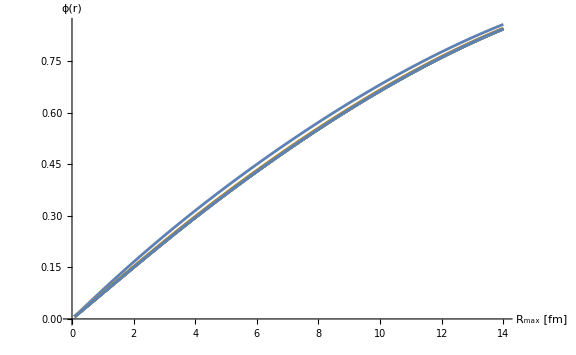

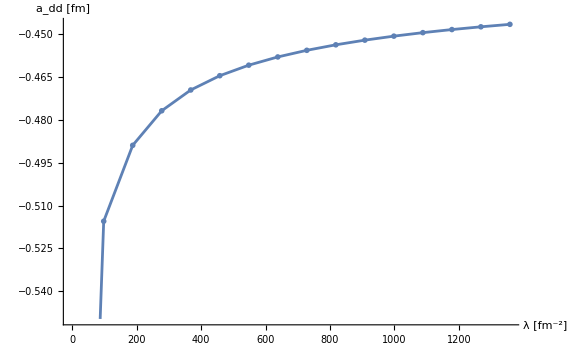

```mathematica
grdPerFermi=12;
rMax=14;
nGrd=IntegerPart[rMax grdPerFermi];
Grd=Range[0,rMax,1/grdPerFermi][[2;;]];

results={};
resultsWF={};
runtimes={};

(*SetSharedVariable[results,resultsPhases];*)
Do[
LECc=Flatten[Select[activeLEC,#[[1]]==lam&]][[2]];
ta=AbsoluteTime[];
{tmp,tmp2}=GetEREP3[lam,rMax,nGrd,dimerCore,LECc,energ];
tb=AbsoluteTime[];
AppendTo[results,tmp];
AppendTo[resultsWF,Transpose[{Grd,tmp2}]];
AppendTo[runtimes,{rMa,(tb-ta)/60.}];
Print["λ = ",lam,"   C_0(λ) = ",LECc,"     R_max = ",rMax,"     #(grid points) = ",nGrd,"                a_dd = ",tmp," fm        a_dd/a_aa = ",Style[tmp/(hbarc/√(Mm Abs[eCore])),Red,18]];
,{lam,lambdas}]

ListPlot[resultsWF,Joined->True,PlotRange->Full,ImageSize->Large,AxesLabel->{"R_max [fm]","ϕ(r)"}]
ListPlot[Transpose[{lambdas,results}],Joined->True,PlotMarkers->"OpenMarkers",AxesLabel->{"λ [fm^-2]","a_dd [fm]"}]
```

-0.43649-(2.18973×10^17)/x^11+(5.40009×10^13)/x^7-(8.47176×10^9)/x^5+362149./x^3-14.5591/x

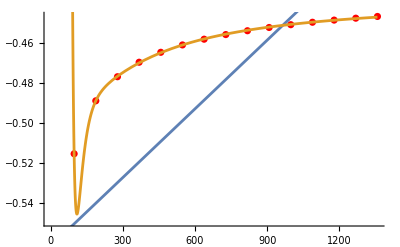

-0.43649

```mathematica
data=Transpose[{lambdas,results}];
line = Fit[data, {1,x},x];
parabola = Fit[data, {1,x^-1,x^-3,x^-5,x^-7,x^-11}, x]
Show[ListPlot[data, PlotStyle->Red], Plot[{line, parabola}, {x,lambdas[[1]],lambdas[[-1]]}]]
Limit[parabola/.x->xx,xx->Infinity]
```

CompiledFunction::cfex: Could not complete external evaluation at instruction 2; proceeding with uncompiled evaluation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

a_dd = -0.877     a_dd/a_aa = -0.201987

CompiledFunction::cfex: Could not complete external evaluation at instruction 2; proceeding with uncompiled evaluation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

a_dd = -0.596988     a_dd/a_aa = -0.137496

CompiledFunction::cfex: Could not complete external evaluation at instruction 2; proceeding with uncompiled evaluation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

a_dd = -0.570477     a_dd/a_aa = -0.13139

CompiledFunction::cfex: Could not complete external evaluation at instruction 2; proceeding with uncompiled evaluation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

a_dd = -0.558417     a_dd/a_aa = -0.128613

CompiledFunction::cfex: Could not complete external evaluation at instruction 2; proceeding with uncompiled evaluation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

a_dd = -0.551159     a_dd/a_aa = -0.126941

CompiledFunction::cfex: Could not complete external evaluation at instruction 2; proceeding with uncompiled evaluation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

a_dd = -0.546181     a_dd/a_aa = -0.125794

CompiledFunction::cfex: Could not complete external evaluation at instruction 2; proceeding with uncompiled evaluation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

a_dd = -0.542496     a_dd/a_aa = -0.124946

CompiledFunction::cfex: Could not complete external evaluation at instruction 2; proceeding with uncompiled evaluation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

a_dd = -0.539626     a_dd/a_aa = -0.124285

CompiledFunction::cfex: Could not complete external evaluation at instruction 2; proceeding with uncompiled evaluation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

a_dd = -0.53731     a_dd/a_aa = -0.123751

CompiledFunction::cfex: Could not complete external evaluation at instruction 2; proceeding with uncompiled evaluation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

a_dd = -0.53539     a_dd/a_aa = -0.123309

CompiledFunction::cfex: Could not complete external evaluation at instruction 2; proceeding with uncompiled evaluation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

a_dd = -0.533764     a_dd/a_aa = -0.122935

CompiledFunction::cfex: Could not complete external evaluation at instruction 2; proceeding with uncompiled evaluation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

a_dd = -0.532365     a_dd/a_aa = -0.122612

CompiledFunction::cfex: Could not complete external evaluation at instruction 2; proceeding with uncompiled evaluation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

a_dd = -0.531144     a_dd/a_aa = -0.122331

CompiledFunction::cfex: Could not complete external evaluation at instruction 2; proceeding with uncompiled evaluation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

a_dd = -0.530066     a_dd/a_aa = -0.122083

CompiledFunction::cfex: Could not complete external evaluation at instruction 2; proceeding with uncompiled evaluation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

a_dd = -0.529105     a_dd/a_aa = -0.121862

CompiledFunction::cfex: Could not complete external evaluation at instruction 2; proceeding with uncompiled evaluation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

a_dd = -0.528243     a_dd/a_aa = -0.121663

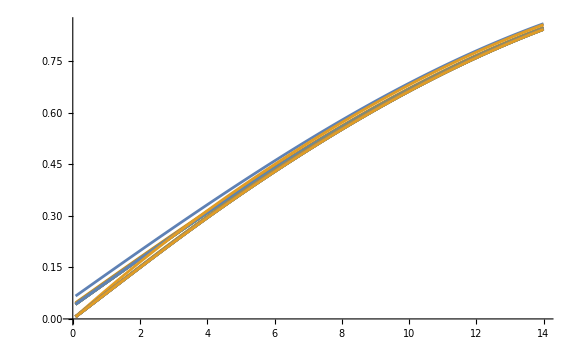

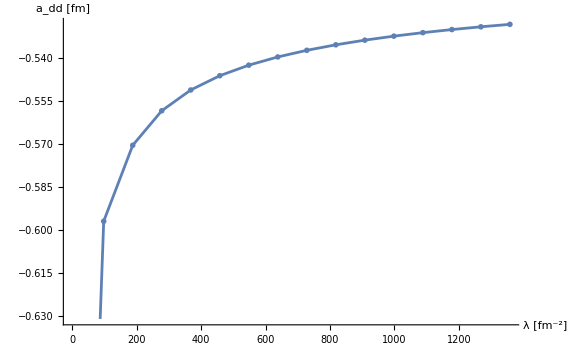

```mathematica
momFM=Sqrt[mh2 energ];
rRan=Range[0,rMax,1/grdPerFermi];
match1=1;
match2=5;
resultsadd={};
riccatis={};
Do[

sol=NSolve[{resultsWF[[nres]][[All,2]][[-match1]]==nm (RiccatiBesselJ[momFM (rMax-match1/grdPerFermi),0]-tandd RiccatiBesselN[momFM (rMax-match1/grdPerFermi),0]),
resultsWF[[nres]][[All,2]][[-match2]]==nm (RiccatiBesselJ[momFM (rMax-match2/grdPerFermi),0]-tandd RiccatiBesselN[momFM (rMax-match2/grdPerFermi),0])},{nm,tandd},Reals];

RiccatiBJN=Table[(nm (RiccatiBesselJ[momFM r,0]-tandd RiccatiBesselN[momFM r,0])),{r,rRan}];
RiccatiBJN=RiccatiBJN/.sol[[1]];
AppendTo[riccatis,Transpose[{rRan,RiccatiBJN}]];

add=(-tandd/.sol[[1]][[2]])/Sqrt[mh2 energ ];
AppendTo[resultsadd,add];

Print["a_dd = ",add, "     a_dd/a_aa = ",add/(hbarc/√(Mm Abs[eCore])) ]
,{nres,Range[Length[lambdas]]}]
ListPlot[Join[riccatis,resultsWF],Joined->True,PlotRange->Full,ImageSize->Large]
ListPlot[Transpose[{lambdas,resultsadd}],Joined->True,PlotMarkers->"OpenMarkers",AxesLabel->{"λ [fm^-2]","a_dd [fm]"}]
```